## Section | Transcendental Roots

The exact roots of transcendental equations can be expressed implicitly as Root objects.

### Exact Roots

The roots of some transcendental functions—nz, nz, z, z, and z—are encountered so regularly that they merit their own “zero” functions.

#### 0x

Plot 0x for 0<=x<=20:

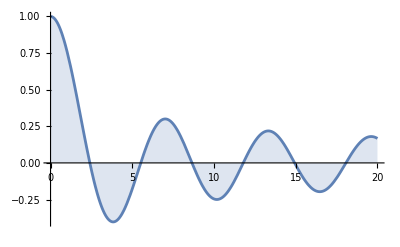

```mathematica
Plot[BesselJ[0,x],{x,0,20},Filling->Axis]
```

Use Solve to compute the exact roots of 0x==0 for 0<=x<=20 as BesselJZero objects:

```mathematica
Solve[{BesselJ[0,x]==0,0≤x≤20},x]
```

{{x→BesselJZero[0,1]},{x→BesselJZero[0,2]},{x→BesselJZero[0,3]},{x→BesselJZero[0,4]},{x→BesselJZero[0,5]},{x→BesselJZero[0,6]}}

#### s

Visualize the first 6 complex zeros of the zeta function, s, in the critical strip using ComplexPlot3D:

```mathematica
ComplexPlot3D[Zeta[s],{s,-1/2+ⅈ,7/2+40 ⅈ},]
```

-Graphics3D-

Using Iconize one can suppress unnecessary detail. Here the list of optional arguments passsed to ComplexPlot3D is represented by the  icon, keeping the focus on the function being plotted.

Use Solve to compute the exact roots of s==0 in the critical strip, where s=σ+ⅈ t, for 0<σ<1 and 1<=t<=40, represented as ZetaZero objects:

```mathematica
Solve[{Zeta[s]==0,0<Re[s]<1&&1≤Im[s]<=40},s]
```

Solve::rhyp: Warning: Solve assumed the Riemann hypothesis in order to prove the solution set found is complete.

{{s→ZetaZero[1]},{s→ZetaZero[2]},{s→ZetaZero[3]},{s→ZetaZero[4]},{s→ZetaZero[5]},{s→ZetaZero[6]}}

This warning message can be ignored as the above plot shows that all 6 roots have been found.

#### 0x+0x

For more general transcendental functions Solve computes the exact roots as (implicitly-defined) Root objects.

Plot 0x+0x for 0<=x<=20:

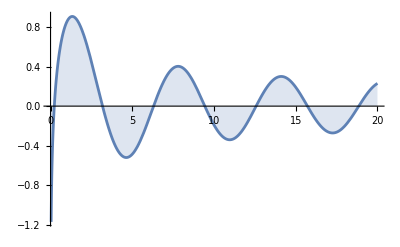

```mathematica
Plot[BesselJ[0,x]+BesselY[0,x],{x,0,20},Filling->Axis]
```

Compute the exact roots of 0x+0x==0 for 0<x<20:

```mathematica
Solve[{BesselJ[0,x]+BesselY[0,x]==0,0<x<20},x]
```

Solve::incs: Warning: Solve was unable to prove that the solution set found is complete.

{{x→},{x→},{x→},{x→},{x→},{x→},{x→}}

This warning message can be ignored as the above plot shows that all 7 roots have been found.

Verify the first root exactly:

```mathematica
BesselJ[0,x]+BesselY[0,x]==0/.x->//FullSimplify
```

True

This computation is exact because, internally, the Root object also stores the function that the root satisfies.

Use InputForm to see the internal form of a Root object:

```mathematica
//InputForm
```

Root[{BesselJ[0, #1] + BesselY[0, #1] & , 0.23033\
0781153665990062542718654510676547792163685476144\
3858`30.102999566398122}]

Evaluate the first root to 200 decimal places:

```mathematica
N[x->,200]
```

x→0.23033078115366599006254271865451067654779216368547614438585140180013505710527122551538124823812830978045947459795267052254315566205927126802053185894846591972425086117244444807447028400991451344459099

Verify this root numerically:

```mathematica
BesselJ[0,x]+BesselY[0,x]/.%
```

0.

### Complex Roots

Cauchy's integral theorem states that if f(z) is analytic in some simply connected region ℛ, then

∮_γ f(z)ⅆz==0

for any closed contour γ completely contained in ℛ. The roots of a function g(z) can be determined by locating the singularities of the reciprocal of the function, h(z)=1/g(z). If h(z) has a simple pole at z_0, then f(z)=(z-z_0)h(z) is analytic. Luck and Stevens (2002) use this to obtain an explicit expression for the root z_0 of g(z),

∮_γ (z-z_0)h(z)ⅆz==0⇒z_0==(∮_γ z h(z)ⅆz)/(∮_γ h(z)ⅆz),

where the contour γ contains the single pole at z_0. We see that the roots are, essentially, the normalized (complex) first moment or mean of h(z).

#### Numerical Integration

To determine the second root of f(z):=0z+0z, use equation (DisplayFormulaNumbered), integrating around an arbitrary (here diamond-shaped) contour enclosing just this root.

Define f(z):

```mathematica
f[z_]:=BesselJ[0,z]+BesselY[0,z]
```

Define h(z):

```mathematica
h[z_]:=1/f[z]
```

Visualize the second zero of f(z):=0z+0z using ComplexPlot3D:

```mathematica
ComplexPlot3D[f[z],{z,1-2 ⅈ,5+2 ⅈ},Mesh->8,MeshStyle->{White,Gray},PlotPoints->25]
```

-Graphics3D-

Use equation (DisplayFormulaNumbered), numerically integrate around an arbitrary (here diamond-shaped) contour enclosing just the second root using NIntegrate:

```mathematica
root[2]=NIntegrate[z h[z],{z,1,3-2ⅈ,5,3+2ⅈ,1}]/NIntegrate[h[z],{z,1,3-2ⅈ,5,3+2ⅈ,1}]
```

3.17929-2.60614×10^-16 ⅈ

Apply f to this root:

```mathematica
f[root[2]]
```

4.54414×10^-13+1.65831×10^-16 ⅈ

Chop uses a default tolerance of 10^-10 to eliminate numbers close to 0:

```mathematica
Chop[%]
```

0

### References

Rogelio Luck and James W. Stevens, “Explicit Solutions for Transcendental Equations”, 2002